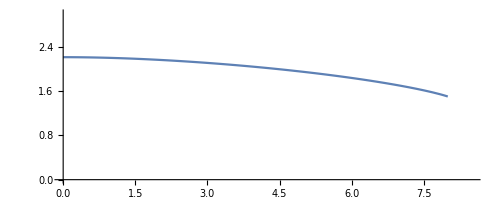

```mathematica
ν=0.03;
ϵ=0.002;
thickness=1.5;
radius=8;
start= 0.000000000001;

eq1=ρ/1 D[ρ((D[r2[ρ],ρ])+(ν r2[ρ])/1+1/2 ρ(D[z1[ρ], ρ])^2), ρ]-ν/1 ρ(D[r2[ρ],ρ]+1/2(D[z1[ρ], ρ])^2)-r2[ρ]/1==0;
eq2=1/1 D[1(D[z1[ρ], ρ])(D[r2[ρ],ρ]ρ+ν r2[ρ]/1+1/2(D[z1[ρ], ρ])^2 ρ), ρ]==-ρ;
s=NDSolve[{eq1, eq2, r2[1]==0,z1[1]==0,(D[z1[ρ], ρ]/.ρ->0)==0 , r2[start]==0},{r2, z1},{ρ,start,1}];
(*simplethickness plot*)
expr0 = {radius*(ρ+ϵ^(2/3) r2[ρ]),radius*(ϵ^(1/3)z1[ρ])+thickness};
ParametricPlot[{Evaluate[expr0/.s]}, {ρ, start, 1}, PlotRange->{{0, 8.5},{0, 3}}]


(*ParametricPlot[{Evaluate[{radius*(1+ϵ^(2/3)r2'[ρ]),radius*(ϵ^(1/3)z1'[ρ])}/.s]}, {ρ, start, 1}, PlotRange->Full]*)
(*ParametricPlot[Evaluate[r2[ρ], z1[ρ]]/.s, {ρ, 0.1, 1}]*)
```

```mathematica
(*Average height for beam spot*)
beamspot = 4;
upperlimit = FindRoot[Interpolation[Transpose[Transpose[Table[Evaluate[expr0/.s], {ρ, start, 1, 0.001}]][[1]]][[1]]][x]-beamspot, {x, 100}](*find end of interpolation with a given beamspot*)
Interpolation[Transpose[Transpose[Table[Evaluate[expr0/.s], {ρ, start, 1, 0.001}]][[1]]][[1]]][499]
Interpolation[Transpose[Transpose[Table[Evaluate[expr0/.s], {ρ, start, 1, 0.001}]][[1]]][[2]]][499]
Interpolation[Transpose[Transpose[Table[Evaluate[expr0/.s], {ρ, start, 1, 0.001}]][[1]]][[1]]][1]
Interpolation[Transpose[Transpose[Table[Evaluate[expr0/.s], {ρ, start, 1, 0.001}]][[1]]][[2]]][1]
Interpolation[Transpose[Transpose[Table[Evaluate[expr0/.s], {ρ, start, 1, 0.001}]][[1]]][[2]]][1]*2 (*max thickness*)
```

{x→498.992}

4.00006

2.0339

8.×10^-12

2.20916

4.41831

{sig→4.80449}

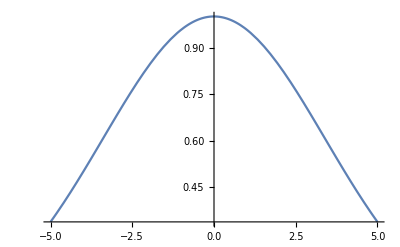

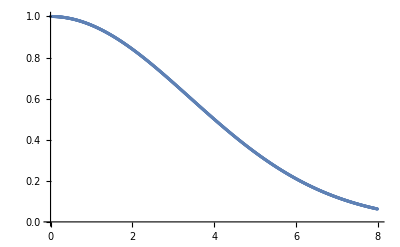

```mathematica
root =FindRoot[Exp[-(beamspot/(sig))^2]-0.5, {sig, 4}]

gauss = Table[{ρ*radius,Exp[-((ρ*radius)/(4.804489635145799))^2]}, {ρ, start, 1, 0.001}];

Plot[{Exp[-(x/(4.804489635145799))^2]}, {x, -5, 5}](*place root here*)
ListPlot[gauss]
(*ρ=x*498.9923674182382/4, dρ =498.9923674182382/4 dx *)
```

```mathematica
integral = N[With[{
	X=Interpolation[ Transpose[Transpose[Table[Evaluate[expr0/.s], {ρ, start, 1, 0.001}]][[1]]][[1]]],
	Y=Interpolation[Transpose[Transpose[Table[Evaluate[expr0/.s], {ρ, start, 1, 0.001}]][[1]]][[2]]],
ga = Interpolation[Table[Exp[-((ρ*radius)/(4.804489635145799))^2], {ρ, start, 1, 0.001}]]
}, Integrate[Y[t]*X[t]* D[X[t],t],{t, 1, 498.9923674182382} ]]]
mean3d = 4/beamspot^2*integral(*avg thickness with given beamspot*)
```

16.9432

4.2358

```mathematica
(*thickness as a function of angle from normal*)
expr1 = {ArcTan[radius*(ρ+ϵ^(2/3) r2[ρ])/(radius*(ϵ^(1/3)z1[ρ])+thickness)],√((radius*(ρ+ϵ^(2/3) r2[ρ]))^2+(radius*(ϵ^(1/3)z1[ρ])+thickness)^2)};
p1 = ParametricPlot[{Evaluate[expr1/.s]}, {ρ, start, 1}, PlotRange->{{0, 3},{1,10 }}];
p2 = Plot[thickness/Cos[θ], {θ, 0, 1.5}, PlotStyle->Red];
Show[p1, p2, Plot]

Export["thickness.txt",Table[Evaluate[expr1/.s], {ρ, start, 2.0, 0.001}]]
```

-Graphics-

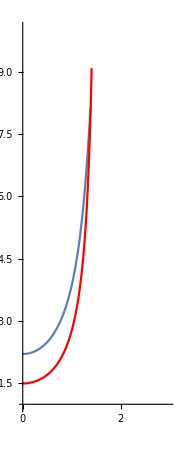

```mathematica
Show[%60,ImageSize->Small]
```

```mathematica
Show[%60,AxesLabel->{HoldForm[Angle[rad]],HoldForm[Half-target thickness[mm]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

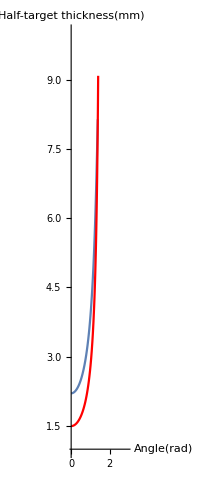

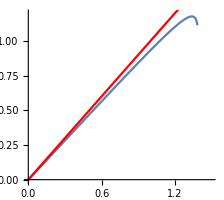

```mathematica
(*havar entrance angle as a function of angle from normal*)
expr2 = {ArcTan[radius*(ρ+ϵ^(2/3) r2[ρ])/(radius*(ϵ^(1/3)z1[ρ])+thickness)],π/2-ArcCos[((radius*(ρ+ϵ^(2/3) r2[ρ])*radius*(1+ϵ^(2/3) D[r2[ρ], ρ])+(radius*(ϵ^(1/3)z1[ρ])+thickness)*radius*(ϵ^(1/3)D[z1[ρ], ρ]))/(√((radius*(ρ+ϵ^(2/3) r2[ρ]))^2+(radius*(ϵ^(1/3)z1[ρ])+thickness)^2)*√((radius*(1+ϵ^(2/3) D[r2[ρ], ρ]))^2+(radius*(ϵ^(1/3)D[z1[ρ], ρ]))^2)))]};
p3 = ParametricPlot[{Evaluate[expr2/.s]}, {ρ, start, 1}, PlotRange->{{0, 1.5},{0,1.2}}];
p4 = Plot[θ, {θ, 0, 1.5}, PlotStyle->Red];
Show[p3, p4]
Table[Evaluate[expr2/.s], {ρ, start, 1.5, 0.001}]
```